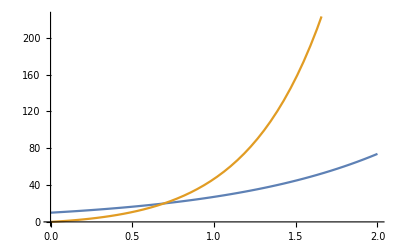

{{73.8905609893},{5931.90594266},{472.090939342}}

```mathematica
ClearAll["Global`*"]
(*0 -> A, A -> 0*)
(*NOTE: x*x ≠ xsq*)

eqns={x'[t]==x[t],
xsq'[t]==2xsq[t]+x[t],
x[0]==10,xsq[0]==10^2};
sol=DSolve[eqns,{x,xsq},t];
Plot[{x[t]/.sol,xsq[t]-x[t]^2/.sol},{t,0,2}]
N[{x[t]/.sol,xsq[t]/.sol,xsq[t]-x[t]^2/.sol}/.{t->2},12]
```